Часть 1. За период 1999-2004 г.г. известен товарооборот (млн. усл. ед.) регионального склада. Сделать прогноз.

```mathematica
TableForm[{{1999,70},{2000,100},{2001,140},{2002,180},{2003,200},{2004,240}}]
```

1999 | 70
2000 | 100
2001 | 140
2002 | 180
2003 | 200
2004 | 240

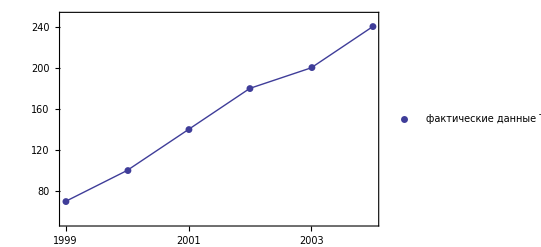

```mathematica
DateListPlot[{70,100,140,180,200,240},{1999}, Joined->True,PlotRange->{50,250},PlotLegends->{"фактические данные T"}, PlotMarkers->Automatic,GridLines->{Automatic,{70,100,140,180,200,240}}]
```

Автор утверждает что товарооборот изменяется в гиперболической зависимости. Поверим ему, но станем использовать предиущий способ расчёта, а заменим его на более удобный.
y = a+b/x

```mathematica
Fit[{70,100,140,180,200,240},{1,x},x]
```

36.+34. x

```mathematica
(35.99999999999997+34.000000000000014  #)&/@{1,2,3,4,5,6}
```

{70.,104.,138.,172.,206.,240.}

```mathematica
Total[%]
```

930.

В то время как реальный товарооборот в сумме составляет:

```mathematica
Total[{70,100,140,180,200,240}]
```

930

Тоесть, как мы видим, уравнение прямой идеально подошло :-)

Спрогнозируем товарооборот ещё и на 2005 и 2006 года:

```mathematica
(35.99999999999997+34.000000000000014  #)&/@{1,2,3,4,5,6,7,8}
```

{70.,104.,138.,172.,206.,240.,274.,308.}

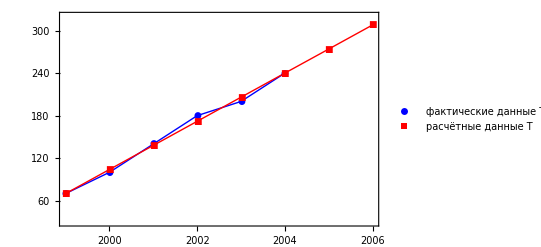

```mathematica
DateListPlot[{{70,100,140,180,200,240}, {69.99999999999999,104.,138.,172.00000000000003,206.00000000000003,240.00000000000006,274.0000000000001,308.0000000000001}},{1999}, Joined->True,PlotRange->{30,320},PlotLegends->{"фактические данные T","расчётные данные T"},PlotStyle->{Blue,Red},PlotMarkers->Automatic,GridLines->{Automatic,{70,100,140,180,200,240}}]
```

Часть 2. Проведём прогноз объёма перевозок с регионального склада с учётом влияния на него различных показателей. Прогнозирование возможно 2 способами:

```mathematica
Q = H×T;
```

```mathematica
Q=(H×YПлановый×(1-MПлановый))/(Y×(1-M))×T;
```

Товарооборот, млн. усл. ед.

```mathematica
T2={70,100,140,180,200,240};
```

Объём перевозок, тыс. тонн

```mathematica
Q= {210,380,616,846,1000,1248};
```

Удельный показатель объёма перевозок, отнесённый на 1 тыс. усл. ед товарооборота, т/млн. усл. ед.

```mathematica
H={3000,3800,4400,4700,5000,5200};
```

Удельный вес децентрализованных перевозок груза автотранспортом, %

```mathematica
M = {30,25,20,15,10,10};
```

Причем, плановый удельный показатель децентрализованных перевозок приймем:

```mathematica
MПлановый=15;
```

Уровень механизации работ при погрузке и разгрузке груза, %

```mathematica
Y = {80,82,85,85,86,87};
```

Причем, плановый уровень механизации работ при погрузке и разгрузке груза:

```mathematica
YПлановый=85;
```

Первый вариант расчёта. Исследуем динамический ряд H.

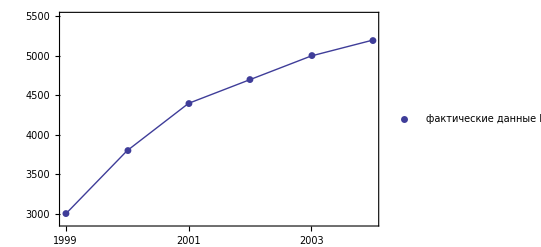

```mathematica
DateListPlot[{3000,3800,4400,4700,5000,5200},{1999}, Joined->True,PlotRange->{2900,5500},PlotLegends->{"фактические данные H"}, PlotMarkers->Automatic,PlotRange->All,GridLines->{Automatic,{3000,3800,4400,4700,5000,5200}}]
```

Динамика даёт нам основание утверждать, что изменение этого показателя по годам имеет вид гиперболы. Дальнейший расчёт проводим по уже знакомой схеме.

```mathematica
H = a+b/x;
```

```mathematica
Fit[H,{1,1/x},x]
```

5388.91-2544.27/x

```mathematica
(5388.910891089108-2544.2715700141503/#)&/@{1,2,3,4,5,6,7,8}
```

{2844.64,4116.78,4540.82,4752.84,4880.06,4964.87,5025.44,5070.88}

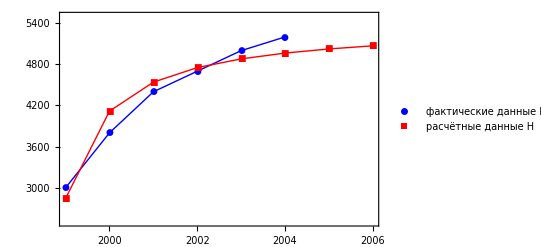

```mathematica
DateListPlot[{H, {2844.639321074958,4116.775106082033,4540.820367751058,4752.842998585571,4880.056577086278,4964.865629420083,5025.44352394423,5070.87694483734}},{1999}, Joined->True,PlotRange->{2500,5500},PlotLegends->{"фактические данные H","расчётные данные H"},PlotStyle->{Blue,Red},PlotMarkers->Automatic,PlotRange->All,GridLines->{Automatic,H}]
```

Тогда, используя прогнозированный товарооборот Т в предыдущей части, можем найти прогнозируемый объём перевозок Q в тоннах, умножив его на соответствующие значения H:

```mathematica
Q прогнозируемое n-го года = H прогнозируемое n × T прогнозируемое n;
```

```mathematica
{2844.639321074958,4116.775106082033,4540.820367751058,4752.842998585571,4880.056577086278,4964.865629420083,5025.44352394423,5070.87694483734}×{69.99999999999999,104.,138.,172.00000000000003,206.00000000000003,240.00000000000006,274.0000000000001,308.0000000000001}
```

{199125.,428145.,626633.,817489.,1.00529×10^6,1.19157×10^6,1.37697×10^6,1.56183×10^6}

```mathematica
%/1000
```

{199.125,428.145,626.633,817.489,1005.29,1191.57,1376.97,1561.83}

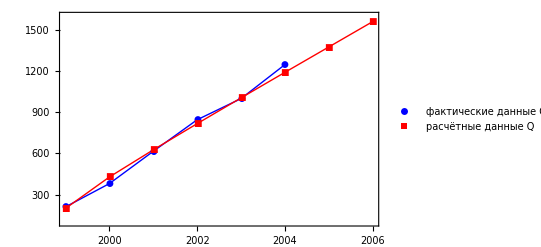

```mathematica
DateListPlot[ {Q, {199.12475247524702,428.14461103253143,626.6332107496461,817.4889957567184,1005.2916548797734,1191.5677510608202,1376.9715255607198,1561.830099009901}},{1999}, Joined->True,PlotRange->{100,1600},PlotLegends->{"фактические данные Q","расчётные данные Q"},PlotStyle->{Blue,Red},PlotMarkers->Automatic,PlotRange->All,GridLines->{Automatic, Q}]
```

Второй вариант расчёта. Как показывает практика, на объём перевозок оказывает влияние уровень механизации погрузочных работ Y и удельный вес децентрализованных перевозок M.
Допустим, что мы уже провели расчёты и спрогнозировали, используя гиперболу как уравнение, описывающее динамический ряд, и получили в 2006 г. М равное 11,65%. Плановый удельный вес нам уже известен, 15%.
Допустим, что мы уже провели расчёты и спрогнозировали, используя прямую как уравнение, описывающее динамический ряд, и получили в 2006 г. Y равное 87,55%. Плановый уровень механизации нам уже известен, 85%.
Используя полученные данные найдём объём перевозок на 2006 г. в тоннах:

```mathematica
Q=(H×YПлановый×(1-MПлановый))/(Y×(1-M))×T;
```

```mathematica
Q2006=(5070.87694483734×0.85×(1-0.15))/(0.8755×(1-0.1165))×308.0000000000001
```

1.45884×10^6

Как мы видим, с учётом влияния децентрализованных перевозок и механизации погрузочно-разгрузочных работ прогноз материалопотока упал на тыс. тонн:

```mathematica
%/1000
```

1458.84

```mathematica
1561.830099009901-1458.8442746560913
```

102.986

Поэтому, важность данных показателей доказана и их всегда следует учитывать.